```mathematica
Plot3D[0.5-Cos[q1]Sin[q2]/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90}]
```

-Graphics3D-

```mathematica
Plot3D[0.5-Sin[q1]Sin[q2]/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90}]
```

-Graphics3D-

```mathematica
Plot3D[(0.9+Sin[q1]Sin[q2])^2+(0.9+Cos[q1]Sin[q2])^2/.{q1->Q1*3.14/180,q2->Q2*3.14/180},{Q1,-180,180},{Q2,-90,90}]
```

-Graphics3D-

```mathematica
ContourPlot[Abs[Cos[0.0175 *Q1] Sin[0.0175*Q2]]+Abs[Sin[0.0175 *Q1] Sin[0.0175*Q2]]==0,{Q1,-180,180},{Q2,-90,90},PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
(0.2+Sin[q1]Sin[q2])^2+(0.0+Cos[q1]Sin[q2])^2==0/.{q1->Q1*3.15/180,q2->Q2*3.15/180}
```

(0.+Cos[0.0175 Q1] Sin[0.0175 Q2])^2+(0.2+Sin[0.0175 Q1] Sin[0.0175 Q2])^2==0

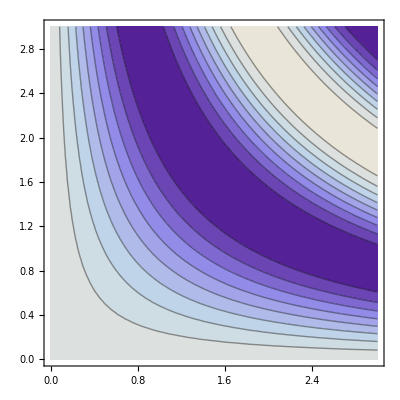

```mathematica
ContourPlot[Sin[x y+10^16],{x,0,3},{y,0,3},WorkingPrecision->20]
```